```mathematica
PolynomialQuotientRemainder[x^4+2 x+1,x^2+1,x]
```

{-1+x^2,2+2 x}

```mathematica
PolynomialQuotientRemainder[x^3,a x+b,x]
```

{b^2/a^3-(b x)/a^2+x^2/a,-b^3/a^3}

```mathematica
ℱ=FiniteField[17,3];
```

```mathematica
PolynomialQuotientRemainder[ℱ[1] x^5+ℱ[123] x+ℱ[456],ℱ[789] x^3+ℱ[987] x+ℱ[654],x]
```

{(x^2 FiniteField[17,3][1])/(FiniteField[17,3][789])-(FiniteField[17,3][1] FiniteField[17,3][987])/(FiniteField[17,3][789])^2,FiniteField[17,3][456]-(x^2 FiniteField[17,3][1] FiniteField[17,3][654])/(FiniteField[17,3][789])+(FiniteField[17,3][1] FiniteField[17,3][654] FiniteField[17,3][987])/(FiniteField[17,3][789])^2+x (FiniteField[17,3][123]+(FiniteField[17,3][1] (FiniteField[17,3][987])^2)/(FiniteField[17,3][789])^2)}

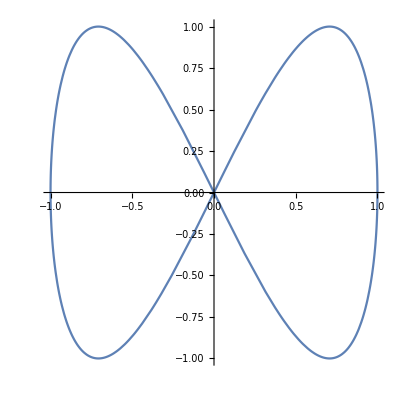

```mathematica
ParametricPlot[{Sin[u],Sin[2 u]},{u,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->{Red,Green}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{6 Cos[u] (1+Sin[u]),16 Sin[u],0}+2 (2-Cos[u]) {Cos[Clip[u,{0,π}]] Cos[v],Sin[Clip[u,{0,π}]] Cos[v],Sin[v]},{u,0,2 π},{v,0,2 π},Lighting->"Classic",Mesh->False,PlotStyle->Opacity[2/3,ColorData["Legacy","AliceBlue"]]]
```

-Graphics3D-

```mathematica
PolynomialQuotientRemainder[ax^2+bx,x+1,x]
```

{0,ax^2+bx}

```mathematica
ParametricPlot[(1-t^2)/(1+t^2),2t/(1+t^2),{t,-10,10}]
```

System`SampledPlotsDump`iParametricPlot[(1-t^2)/(1+t^2),(2 t)/(1+t^2),{t,-10,10}]

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[x]^3 Sin[y],Cos[x] Cos[y],Tan[x]},{x,0,1},{y,-Pi,Pi}]
```

-Graphics3D-